```mathematica
sol=NDSolve[{y1'[t]==y2[t],y2'[t]==100(1-y1[t]^2)y2[t]-y1[t],y1[0]==2,y2[0]==0},{y1[t],y2[t]},{t,0,350}];

y1s=y1[t]/.sol[[1]];
y2s=y2[t]/.sol[[1]];
```

InterpolatingFunction[{{0.,350.}},<>][t]

InterpolatingFunction[{{0.,350.}},<>][t]

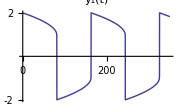

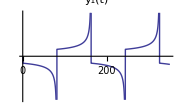

/Users/maba/Documents/hs-bochum/07-MaGruNum/03-aufgaben/_00-pics/vanderpol.pdf

```mathematica
g1=Plot[y1s,{t,0,350},Ticks->{Table[i,{i,0,350,100}],{-2,2}},PlotStyle->AbsoluteThickness[1],ImageSize->180,PlotLabel->"y_1(t)"]
g2=Plot[y2s,{t,0,350},Ticks->{Table[i,{i,0,350,100}],{-2,2}},PlotStyle->AbsoluteThickness[1],ImageSize->180,PlotLabel->"y_1(t)"]

Export[NotebookDirectory[]<>"vanderpol.pdf",g1]
```